```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

## Fastest Descending

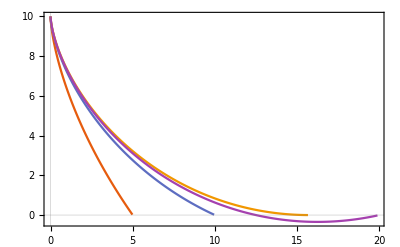

../figure/fastest-descedning.png

```mathematica
parmset1={H->10,L->5};
parmset2={H->10,L->10};
parmset3={H->10,L->Pi/2*10};
parmset4={H->10,L->20};


g=QuantityMagnitude[UnitConvert[Quantity["StandardAccelerationOfGravity"]]];
eqns={H==Sin[theta]^2/C^2,C^2*L==theta-1/2*Sin[2*theta]};
sol1=FindRoot[eqns/.parmset1,{{C,0.1},{theta,0.9}}];
sol2=FindRoot[eqns/.parmset2,{{C,0.1},{theta,0.9}}];
sol3=FindRoot[eqns/.parmset3,{{C,0.1},{theta,0.9}}];
sol4=FindRoot[eqns/.parmset4,{{C,0.1},{theta,0.9}}];

xparm=1/C^2(Sqrt[2*g]/2*C*t-1/2*Sin[2*(Sqrt[2*g]/2*C*t)]);
yparm=H-Sin[Sqrt[2*g]/2*C*t]^2/C^2;
tmaxfun[C_,theta_]:=2/(Sqrt[2*g]*C)*theta;

generateLine[sol_,parm_]:=Table[{Evaluate[xparm/.(sol~Join~parm)],Evaluate[yparm/.(sol~Join~parm)]},{t,0,(tmaxfun[C,theta]/.sol),0.01}]
line1=generateLine[sol1,parmset1];
line2=generateLine[sol2,parmset2];
line3=generateLine[sol3,parmset3];
line4=generateLine[sol4,parmset4];

$PlotTheme="Scientific";
plot=ListLinePlot[{line1,line2,line3,line4},PlotLegends->{MaTeX["H=10,L=5"],MaTeX["H=10,L=10"],MaTeX["H=10,L=\\frac{\\pi}{2}H"],MaTeX["H=10,L=20"]}]
Export["../figure/fastest-descedning.png",plot]
```

```mathematica
Pi/2*10//N
```

15.708

```mathematica
sol4
```

{C→0.316228,theta→1.5708}

```mathematica
1/Sqrt[10]//N
```

0.316228

## Fastest Ascending

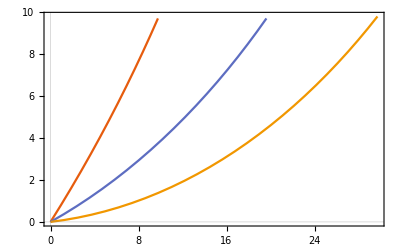

../figure/fastest-ascedning.png

```mathematica
parmset1={v0->25,H->10,L->10};
parmset2={v0->25,H->10,L->20};
parmset3={v0->25,H->10,L->30};

g=QuantityMagnitude[UnitConvert[Quantity["StandardAccelerationOfGravity"]]];
eqns={C^2*v0^2/(2*g)==Sin[theta0]^2,C^2*(v0^2/(2*g)-H)==Sin[theta1]^2,
C1==-(theta0-1/2*Sin[2*theta0]),C^2*L+C1==-(theta1-1/2*Sin[2*theta1])};
sol1=FindRoot[eqns/.parmset1,{{C,0.1},{C1,0.1},{theta0,1.5},{theta1,0.5}}];
sol2=FindRoot[eqns/.parmset2,{{C,0.1},{C1,0.1},{theta0,1.5},{theta1,0.5}}];
sol3=FindRoot[eqns/.parmset3,{{C,0.1},{C1,0.1},{theta0,1.5},{theta1,0.5}}];

xparm=-1/C^2(theta0-Sqrt[2*g]/2*C*t-1/2*Sin[2*(theta0-Sqrt[2*g]/2*C*t)]+C1);
yparm=v0^2/(2*g)-Sin[theta0-Sqrt[2*g]/2*C*t]^2/C^2;
tmaxfun[C_,theta0_,theta1_]:=2/(Sqrt[2*g]*C)*(theta0-theta1);

generateLine[sol_,parm_]:=Table[{Evaluate[xparm/.(sol~Join~parm)],Evaluate[yparm/.(sol~Join~parm)]},{t,0,(tmaxfun[C,theta0,theta1]/.sol),0.05}]
line1=generateLine[sol1,parmset1];
line2=generateLine[sol2,parmset2];
line3=generateLine[sol3,parmset3];


$PlotTheme="Scientific";
plot=ListLinePlot[{line1,line2,line3},PlotLegends->{MaTeX["v_0=25,H=10,L=10"],MaTeX["v_0=25,H=10,L=20"],MaTeX["v_0=25,H=10,L=30"]}]
Export["../figure/fastest-ascedning.png",plot]
```